```mathematica
(*Mathematica*)
```

```mathematica
(*Bonacci 6*)
p[x_]=ExpandAll[1-x+2*x^2+x^4-x^5+x^6]
```

1-x+2 x^2+x^4-x^5+x^6

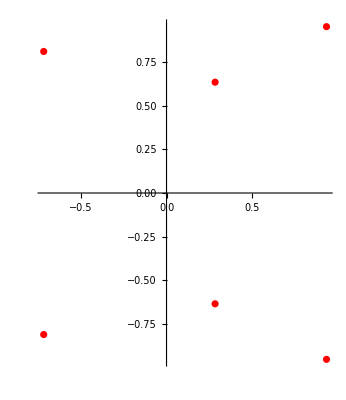

```mathematica
ComplexListPlot[z/.NSolve[p[z]==0,z],PlotStyle->Red]
```

```mathematica
ϕ=N[GoldenRatio];
r[i_]:=x/.NSolve[p[x]==0,x][[i]]
sc=2.0;
```

```mathematica
f[z_]=Exp[2*π*I*ϕ]*z^12*(z^2-(sc*r[1])^2)*(z^2-(sc*r[2])^2)*(z^2-(sc*r[3])^2)*(z^2-(sc*r[4])^2)*(z^2-(sc*r[5])^2)*(z^2-(sc*r[6])^2)/((-(sc*r[1]*z)^2+1)*(-(sc*r[2]*z)^2+1)*(-(sc*r[3]*z)^2+1)*(-(sc*r[4]*z)^2+1)*(-(sc*r[5]*z)^2+1)*(-(sc*r[6]*z)^2+1))
```

-((0.737369+0.67549 ⅈ) z^12 ((0.141872-7.10121 ⅈ)+z^2) ((0.141872+7.10121 ⅈ)+z^2) ((0.571695-4.63806 ⅈ)+z^2) ((0.571695+4.63806 ⅈ)+z^2) ((1.28643-1.43632 ⅈ)+z^2) ((1.28643+1.43632 ⅈ)+z^2))/((1+(0.141872-7.10121 ⅈ) z^2) (1+(0.141872+7.10121 ⅈ) z^2) (1+(0.571695-4.63806 ⅈ) z^2) (1+(0.571695+4.63806 ⅈ) z^2) (1+(1.28643-1.43632 ⅈ) z^2) (1+(1.28643+1.43632 ⅈ) z^2))

```mathematica
g0=JuliaSetPlot[f[z],z, Method -> "OrbitDetection",ColorFunction->Hue,ImageSize->2000,PlotStyle->{PointSize[0.0005]},AspectRatio->1,ImageResolution->2000,PerformanceGoal->"Quality","Bound"->12,Frame->False,PlotRange->All];
```

#### 3D and plane Mandelbrots/ Julias

```mathematica
(*Julia with SQRT(x^2+y^2) limited measure*)
(*by Roger Lee .10Bagula 18 July 2023 © *)
numberOfz2ToEscape[z_] := Block[
	{escapeCount, nz = N[z],nn=4,nzold=0},
	For[
		escapeCount = 0,
		(Abs[nz]<64) && (escapeCount < 2048) &&(Abs[nz-nzold]>0.5*10^(-3)),
		nzold=nz;
		nz=f[nz];
		++escapeCount
	];
	
	escapeCount*If[(Abs[nz-nzold]>10^(-3)),escapeCount*(2*Pi-Abs[ArcTan[nz]+I*ArcTan[nz]*Tan[1]-Arg[z]]),escapeCount*(2*Pi-Arg[nz]*(Max[1-Arg[nz]/(2*Pi),Arg[nz]/(2*Pi)]))]
	
	
]
```

```mathematica
FractalPureM[{{ReMin_, ReMax_, ReSteps_},
			 {ImMin_, ImMax_, ImSteps_}}] :=
		ParallelTable[
			numberOfz2ToEscape[x + y I],
			{y, ImMin, ImMax, (ImMax - ImMin)/ImSteps},
			{x, ReMin, ReMax, (ReMax - ReMin)/ReSteps}
		
	]
```

```mathematica
arraym=FractalPureM[{{-2.75001,2.75,1000},{-2.5001,2.75,1000}}];
```

CloudConnect::vwarn: This version of Mathematica will no longer be supported for use with the Wolfram Cloud beginning Tue 1 Jul 2025. Please

General::munfl: (1.06642×10^-30+2.53946×10^-30 ⅈ)^12 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (2.10533×10^-31-1.96808×10^-31 ⅈ)^12 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (4.61356×10^-28+4.88741×10^-28 ⅈ)^12 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: (-2.25637×10^-31-1.70374×10^-30 ⅈ)^12 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (1.04939×10^-34+3.97762×10^-35 ⅈ)^12 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (1.05449×10^-32-6.88121×10^-33 ⅈ)^12 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (6.30999×10^-32+7.99395×10^-32 ⅈ)^12 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: (2.37477×10^-28+5.03328×10^-30 ⅈ)^12 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (1.4291×10^-31-3.64403×10^-32 ⅈ)^12 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: (3.88157×10^-31+3.85688×10^-31 ⅈ)^12 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (2.05306×10^-36-3.00737×10^-36 ⅈ)^12 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (-3.17573×10^-32+3.26448×10^-31 ⅈ)^12 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: (3.9374×10^-34+2.46879×10^-34 ⅈ)^12 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (6.88601×10^-30-8.64985×10^-29 ⅈ)^12 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (1.94159×10^-31-4.98399×10^-31 ⅈ)^12 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: (-7.65246×10^-28+1.16653×10^-28 ⅈ)^12 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (4.38895×10^-31-1.59532×10^-31 ⅈ)^12 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (-1.60427×10^-28-1.69158×10^-29 ⅈ)^12 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: (-7.77923×10^-31+2.16517×10^-30 ⅈ)^12 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (9.1727×10^-32+1.05298×10^-31 ⅈ)^12 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (-1.47139×10^-27-7.21929×10^-29 ⅈ)^12 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: (-5.56128×10^-31-6.03692×10^-31 ⅈ)^12 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (1.08841×10^-29-1.58027×10^-29 ⅈ)^12 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (-1.16231×10^-32+4.28247×10^-33 ⅈ)^12 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: (2.21576×10^-36-4.06988×10^-36 ⅈ)^12 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (2.32019×10^-33+1.09078×10^-31 ⅈ)^12 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (3.41972×10^-33-8.91531×10^-33 ⅈ)^12 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: (-4.91169×10^-31-1.98306×10^-30 ⅈ)^12 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (-1.33656×10^-29+8.34018×10^-30 ⅈ)^12 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (6.52803×10^-29+1.66249×10^-28 ⅈ)^12 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: (7.59708×10^-29-2.00555×10^-28 ⅈ)^12 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (-4.9894×10^-29-8.81994×10^-28 ⅈ)^12 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (7.99176×10^-32+3.42802×10^-29 ⅈ)^12 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: (2.65914×10^-31+1.22362×10^-30 ⅈ)^12 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (-7.24847×10^-35+3.26183×10^-35 ⅈ)^12 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (1.15558×10^-27-2.38764×10^-28 ⅈ)^12 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: (2.06615×10^-31-4.17634×10^-30 ⅈ)^12 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (-6.02015×10^-30-8.259×10^-31 ⅈ)^12 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (-3.04566×10^-34+1.92685×10^-35 ⅈ)^12 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: (-1.13588×10^-32+5.58808×10^-32 ⅈ)^12 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (9.37384×10^-30+1.03108×10^-30 ⅈ)^12 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (3.50285×10^-28-1.7044×10^-28 ⅈ)^12 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: (4.21134×10^-29-4.42434×10^-29 ⅈ)^12 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (-5.79522×10^-28-6.26886×10^-28 ⅈ)^12 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (-7.44012×10^-35+1.87943×10^-35 ⅈ)^12 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: (4.42442×10^-31+4.25733×10^-31 ⅈ)^12 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (-2.05009×10^-33+1.50998×10^-33 ⅈ)^12 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (2.08918×10^-27+6.19679×10^-27 ⅈ)^12 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: (1.7018×10^-29-5.65302×10^-30 ⅈ)^12 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (-1.48546×10^-37+3.74061×10^-36 ⅈ)^12 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (2.5723×10^-32-3.66891×10^-31 ⅈ)^12 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: (3.54393×10^-28-1.22521×10^-27 ⅈ)^12 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (8.58451×10^-28+1.15339×10^-27 ⅈ)^12 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (2.73378×10^-31+1.50605×10^-30 ⅈ)^12 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: (1.39958×10^-32-1.04962×10^-32 ⅈ)^12 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (-9.91187×10^-31+2.33135×10^-30 ⅈ)^12 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (-6.64582×10^-36+1.32334×10^-35 ⅈ)^12 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: (1.34771×10^-28+8.92362×10^-28 ⅈ)^12 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (9.44362×10^-29+5.08306×10^-28 ⅈ)^12 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (-4.99178×10^-30-1.56244×10^-29 ⅈ)^12 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: (1.17887×10^-28+1.26048×10^-29 ⅈ)^12 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (-2.21167×10^-36+2.74083×10^-37 ⅈ)^12 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (2.96949×10^-32+5.57737×10^-30 ⅈ)^12 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: (6.759×10^-33+1.91334×10^-32 ⅈ)^12 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (-5.68338×10^-27-1.38328×10^-26 ⅈ)^12 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (6.29281×10^-33+3.07608×10^-33 ⅈ)^12 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

```mathematica
g1=ListPlot3D[N[Log[1/Max[arraym]+arraym]], Mesh -> False,AspectRatio -> Automatic,Boxed->False, Axes->False,ColorFunction->Hue,Background->Black,ViewPoint->Above,ImageSize->2000];
```

```mathematica
g2=ListDensityPlot[arraym,   Mesh -> False,     AspectRatio -> Automatic, ColorFunction->(Hue[(2*#)]&),ImageSize->2000,Axes->False,ImageSize->2000,Frame->False];
```

```mathematica
colortab=Reverse[Union[Sort[Join[Flatten[Delete[Sort[Union[Table[Delete[Sort[Union[Flatten[Table[If[i+j+k==n,{(1)^2,(1-j)^2,(1-k)^2},{}],{i,0,1,1/10},{j,0,1,1/10},{k,0,1,1/10}],2]]],1],{n,0,1,1/30}]]],1],1],{{0,0,0.5625},{0,0,0.625},{0,0,0.6875},{0,0,0.75},{0,0,0.8125},{0,0,0.875},{0,0,0.9375},{0,0,1},{0,0.0625,1},{0,0.125,1},{0,0.1875,1},{0,0.25,1},{0,0.3125,1},{0,0.375,1},{0,0.4375,1},{0,0.5,1},{0,0.5625,1},{0,0.625,1},{0,0.6875,1},{0,0.75,1},{0,0.8125,1},{0,0.875,1},{0,0.9375,1},{0,1,1},{0.0625,1,1},{0.125,1,0.9375},{0.1875,1,0.875},{0.25,1,0.8125},{0.3125,1,0.75},{0.375,1,0.6875},{0.4375,1,0.625},{0.5,1,0.5625},{0.5625,1,0.5},{0.625,1,0.4375},{0.6875,1,0.375},{0.75,1,0.3125},{0.8125,1,0.25},{0.875,1,0.1875},{0.9375,1,0.125},{1,1,0.0625},{1,1,0},{1,0.9375,0},{1,0.875,0},{1,0.8125,0},{1,0.75,0},{1,0.6875,0},{1,0.625,0},{1,0.5625,0},{1,0.5,0},{1,0.4375,0},{1,0.375,0},{1,0.3125,0},{1,0.25,0},{1,0.1875,0},{1,0.125,0},{1,0.0625,0},{1,0,0},{0.9375,0,0},{0.875,0,0},{0.8125,0,0},{0.75,0,0},{0.6875,0,0},{0.625,0,0},{0.5625,0,0}},{{0,0,0.5625},{0,0,0.625},{0,0,0.6875},{0,0,0.75},{0,0,0.8125},{0,0,0.875},{0,0,0.9375},{0,0,1},{0,0.0625,1},{0,0.125,1},{0,0.1875,1},{0,0.25,1},{0,0.3125,1},{0,0.375,1},{0,0.4375,1},{0,0.5,1},{0,0.5625,1},{0,0.625,1},{0,0.6875,1},{0,0.75,1},{0,0.8125,1},{0,0.875,1},{0,0.9375,1},{0,1,1},{0.0625,1,1},{0.125,1,0.9375},{0.1875,1,0.875},{0.25,1,0.8125},{0.3125,1,0.75},{0.375,1,0.6875},{0.4375,1,0.625},{0.5,1,0.5625},{0.5625,1,0.5},{0.625,1,0.4375},{0.6875,1,0.375},{0.75,1,0.3125},{0.8125,1,0.25},{0.875,1,0.1875},{0.9375,1,0.125},{1,1,0.0625},{1,1,0},{1,0.9375,0},{1,0.875,0},{1,0.8125,0},{1,0.75,0},{1,0.6875,0},{1,0.625,0},{1,0.5625,0},{1,0.5,0},{1,0.4375,0},{1,0.375,0},{1,0.3125,0},{1,0.25,0},{1,0.1875,0},{1,0.125,0},{1,0.0625,0},{1,0,0},{0.9375,0,0},{0.875,0,0},{0.8125,0,0},{0.75,0,0},{0.6875,0,0},{0.625,0,0},{0.5625,0,0}}/2,{{0,0,0.5625},{0,0,0.625},{0,0,0.6875},{0,0,0.75},{0,0,0.8125},{0,0,0.875},{0,0,0.9375},{0,0,1},{0,0.0625,1},{0,0.125,1},{0,0.1875,1},{0,0.25,1},{0,0.3125,1},{0,0.375,1},{0,0.4375,1},{0,0.5,1},{0,0.5625,1},{0,0.625,1},{0,0.6875,1},{0,0.75,1},{0,0.8125,1},{0,0.875,1},{0,0.9375,1},{0,1,1},{0.0625,1,1},{0.125,1,0.9375},{0.1875,1,0.875},{0.25,1,0.8125},{0.3125,1,0.75},{0.375,1,0.6875},{0.4375,1,0.625},{0.5,1,0.5625},{0.5625,1,0.5},{0.625,1,0.4375},{0.6875,1,0.375},{0.75,1,0.3125},{0.8125,1,0.25},{0.875,1,0.1875},{0.9375,1,0.125},{1,1,0.0625},{1,1,0},{1,0.9375,0},{1,0.875,0},{1,0.8125,0},{1,0.75,0},{1,0.6875,0},{1,0.625,0},{1,0.5625,0},{1,0.5,0},{1,0.4375,0},{1,0.375,0},{1,0.3125,0},{1,0.25,0},{1,0.1875,0},{1,0.125,0},{1,0.0625,0},{1,0,0},{0.9375,0,0},{0.875,0,0},{0.8125,0,0},{0.75,0,0},{0.6875,0,0},{0.625,0,0},{0.5625,0,0}}/1.5,{{0,0,0.5625},{0,0,0.625},{0,0,0.6875},{0,0,0.75},{0,0,0.8125},{0,0,0.875},{0,0,0.9375},{0,0,1},{0,0.0625,1},{0,0.125,1},{0,0.1875,1},{0,0.25,1},{0,0.3125,1},{0,0.375,1},{0,0.4375,1},{0,0.5,1},{0,0.5625,1},{0,0.625,1},{0,0.6875,1},{0,0.75,1},{0,0.8125,1},{0,0.875,1},{0,0.9375,1},{0,1,1},{0.0625,1,1},{0.125,1,0.9375},{0.1875,1,0.875},{0.25,1,0.8125},{0.3125,1,0.75},{0.375,1,0.6875},{0.4375,1,0.625},{0.5,1,0.5625},{0.5625,1,0.5},{0.625,1,0.4375},{0.6875,1,0.375},{0.75,1,0.3125},{0.8125,1,0.25},{0.875,1,0.1875},{0.9375,1,0.125},{1,1,0.0625},{1,1,0},{1,0.9375,0},{1,0.875,0},{1,0.8125,0},{1,0.75,0},{1,0.6875,0},{1,0.625,0},{1,0.5625,0},{1,0.5,0},{1,0.4375,0},{1,0.375,0},{1,0.3125,0},{1,0.25,0},{1,0.1875,0},{1,0.125,0},{1,0.0625,0},{1,0,0},{0.9375,0,0},{0.875,0,0},{0.8125,0,0},{0.75,0,0},{0.6875,0,0},{0.625,0,0},{0.5625,0,0}}/3,{{0,0,0.5625},{0,0,0.625},{0,0,0.6875},{0,0,0.75},{0,0,0.8125},{0,0,0.875},{0,0,0.9375},{0,0,1},{0,0.0625,1},{0,0.125,1},{0,0.1875,1},{0,0.25,1},{0,0.3125,1},{0,0.375,1},{0,0.4375,1},{0,0.5,1},{0,0.5625,1},{0,0.625,1},{0,0.6875,1},{0,0.75,1},{0,0.8125,1},{0,0.875,1},{0,0.9375,1},{0,1,1},{0.0625,1,1},{0.125,1,0.9375},{0.1875,1,0.875},{0.25,1,0.8125},{0.3125,1,0.75},{0.375,1,0.6875},{0.4375,1,0.625},{0.5,1,0.5625},{0.5625,1,0.5},{0.625,1,0.4375},{0.6875,1,0.375},{0.75,1,0.3125},{0.8125,1,0.25},{0.875,1,0.1875},{0.9375,1,0.125},{1,1,0.0625},{1,1,0},{1,0.9375,0},{1,0.875,0},{1,0.8125,0},{1,0.75,0},{1,0.6875,0},{1,0.625,0},{1,0.5625,0},{1,0.5,0},{1,0.4375,0},{1,0.375,0},{1,0.3125,0},{1,0.25,0},{1,0.1875,0},{1,0.125,0},{1,0.0625,0},{1,0,0},{0.9375,0,0},{0.875,0,0},{0.8125,0,0},{0.75,0,0},{0.6875,0,0},{0.625,0,0},{0.5625,0,0}}/6,{{0,0,0.5625},{0,0,0.625},{0,0,0.6875},{0,0,0.75},{0,0,0.8125},{0,0,0.875},{0,0,0.9375},{0,0,1},{0,0.0625,1},{0,0.125,1},{0,0.1875,1},{0,0.25,1},{0,0.3125,1},{0,0.375,1},{0,0.4375,1},{0,0.5,1},{0,0.5625,1},{0,0.625,1},{0,0.6875,1},{0,0.75,1},{0,0.8125,1},{0,0.875,1},{0,0.9375,1},{0,1,1},{0.0625,1,1},{0.125,1,0.9375},{0.1875,1,0.875},{0.25,1,0.8125},{0.3125,1,0.75},{0.375,1,0.6875},{0.4375,1,0.625},{0.5,1,0.5625},{0.5625,1,0.5},{0.625,1,0.4375},{0.6875,1,0.375},{0.75,1,0.3125},{0.8125,1,0.25},{0.875,1,0.1875},{0.9375,1,0.125},{1,1,0.0625},{1,1,0},{1,0.9375,0},{1,0.875,0},{1,0.8125,0},{1,0.75,0},{1,0.6875,0},{1,0.625,0},{1,0.5625,0},{1,0.5,0},{1,0.4375,0},{1,0.375,0},{1,0.3125,0},{1,0.25,0},{1,0.1875,0},{1,0.125,0},{1,0.0625,0},{1,0,0},{0.9375,0,0},{0.875,0,0},{0.8125,0,0},{0.75,0,0},{0.6875,0,0},{0.625,0,0},{0.5625,0,0}}/12]]]];
```

```mathematica
Length[%]
```

447

```mathematica
cf[l_]:=Block[{niv,rgb},niv=If[l<1/447,1,Ceiling[447*l]];
rgb=colortab[[niv]];
RGBColor[rgb[[1]],rgb[[2]],rgb[[3]]]];
```

```mathematica
g3=Rasterize[ListDensityPlot[Abs[Log[1/Max[arraym]+arraym]], Mesh -> False, AspectRatio -> Automatic, ColorFunction->cf,ImageSize->2000,Frame->False],RasterSize->2000,ImageSize->2000];
```

```mathematica
Export["j_1000_6_3Knot_z12_Herman_rings_3d_Inside_Outside_monitor_grid.jpg",GraphicsGrid[{{g0,g1},{g2,g3}},ImageSize->{{4000,4000}}]]
```

j_1000_6_3Knot_z12_Herman_rings_3d_Inside_Outside_monitor_grid.jpg

```mathematica
(*end*)
```